# IPPT Model

## 3d. 3-Set Data Import, Multiple Pulse

Description:
- This notebook will import the results from “3b. Multiple-Pulse Data Export” for any propellant choice using two input files for steady-state data.
- Results are imported from WDX format from desired file path on PC.

How to Run:
- First, evaluate notebooks 1 and 2b for propellant of choice. Export data using 3b to create a WDX file type.
- Pull the desired three files to “Documents” folder on PC, or to whichever folder Mathematica is auto-tethered.
- Either click “Evaluate Notebook” in Menu Options or import file manually.

## Data Import

Notes:
- Adjust the date the files were produced and the shot numbers to reflect desired data sources

```mathematica
Filename1="2022-02-13_v1.12_run_17.wdx";
Filename2="2022-02-13_v1.12_run_14.wdx";
Filename3="2022-02-07_v1.12_run_9.wdx";

shotdata1 = Import[Filename1];
shotdata2 = Import[Filename2];
shotdata3 = Import[Filename3];
```

## Unpack Data

```mathematica
(** Dataset 1 **)
(* ICs *)
zmax1=shotdata1[[1]];
zsteps1=shotdata1[[2]];
tmax1=shotdata1[[3]];
tsteps1=shotdata1[[4]];
zs01=shotdata1[[5]];
ws01=shotdata1[[6]];
χi01=shotdata1[[7]];
zχi1=shotdata1[[8]];
nn01=shotdata1[[9]];
zn1=shotdata1[[10]];
Te01=shotdata1[[11]];
Ti01=shotdata1[[12]];
Lc1=shotdata1[[13]];
L01=shotdata1[[14]];
Rc1=shotdata1[[15]];
C01=shotdata1[[16]];
V01=shotdata1[[17]];
zc1=shotdata1[[18]];
zc01=shotdata1[[19]];
rout1=shotdata1[[20]];
rin1=shotdata1[[21]];
frep1 = shotdata1[[22]];
Np1 =shotdata1[[23]]; 
(* Per-pulse performance metrics and nondimesionalized parameters *)
Isptable1=shotdata2[[24]];
nttable1=shotdata2[[25]];
ntrectable1=shotdata2[[26]];
nmtable1=shotdata2[[27]];
piion1table1=shotdata2[[28]];
piion2table1=shotdata2[[29]];
picextable1=shotdata2[[30]];
(* Pulse 1 state/performance *)
nni1=shotdata1[[31]];
wsi1=shotdata1[[32]];
zsi1=shotdata1[[33]];
vsi1=shotdata1[[34]];
vfi1=shotdata1[[35]];
nsi1=shotdata1[[36]];
nfi1=shotdata1[[37]];
Ici1=shotdata1[[38]];
Ipi1=shotdata1[[39]];
Mi1=shotdata1[[40]];
Vi1=shotdata1[[41]];
Tei1=shotdata1[[42]];
Tii1=shotdata1[[43]];
psi1=shotdata1[[44]];
KEsi1=shotdata1[[45]];
Efi1=shotdata1[[46]];
mbiti1=shotdata1[[47]];
msi1[t_]=shotdata1[[48]];
Epii1=shotdata1[[49]];
Eeli1=shotdata1[[50]];
Eindi1[t_]=shotdata1[[51]];
Ecapi1[t_]=shotdata1[[52]];
Ekei1[t_]=shotdata1[[53]];
EkePli1[t_]=shotdata1[[54]];
EkeEnti1[t_]=shotdata1[[55]];
Etei1[t_]=shotdata1[[56]];
Ibiti1[t_]=shotdata1[[57]];
Ispi1[t_]=shotdata1[[58]];
ηmi1[t_]=shotdata1[[59]];
MassFraci1[t_]=shotdata1[[60]];
ηTi1[t_]=shotdata1[[61]];
ηTreci1[t_]=shotdata1[[62]];
Πioni1[t_]=shotdata1[[63]];
Πion2i1[t_]=shotdata1[[64]];
Πcex2i1[t_]=shotdata1[[65]];
(* Pulse n state/performance *)
nnf1=shotdata1[[66]];
wsf1=shotdata1[[67]];
zsf1=shotdata1[[68]];
vsf1=shotdata1[[69]];
vff1=shotdata1[[70]];
nsf1=shotdata1[[71]];
nff1=shotdata1[[72]];
Icf1=shotdata1[[73]];
Ipf1=shotdata1[[74]];
Mf1=shotdata1[[75]];
Vf1=shotdata1[[76]];
Tef1=shotdata1[[77]];
Tif1=shotdata1[[78]];
psf1=shotdata1[[79]];
KEsf1=shotdata1[[80]];
Eff1=shotdata1[[81]];
mbitf1=shotdata1[[82]];
msf1[t_]=shotdata1[[83]];
Epif1=shotdata1[[84]];
Eelf1=shotdata1[[85]];
Eindf1[t_]=shotdata1[[86]];
Ecapf1[t_]=shotdata1[[87]];
Ekef1[t_]=shotdata1[[88]];
EkePlf1[t_]=shotdata1[[89]];
EkeEntf1[t_]=shotdata1[[90]];
Etef1[t_]=shotdata1[[91]];
Ibitf1[t_]=shotdata1[[92]];
Ispf1[t_]=shotdata1[[93]];
ηmf1[t_]=shotdata1[[94]];
MassFracf1[t_]=shotdata1[[95]];
ηTf1[t_]=shotdata1[[96]];
ηTrecf1[t_]=shotdata1[[97]];
Πionf1[t_]=shotdata1[[98]];
Πion2f1[t_]=shotdata1[[99]];
Πcex2f1[t_]=shotdata1[[100]];

(** Dataset 2 **)
(* ICs *)
zmax2=shotdata2[[1]];
zsteps2=shotdata2[[2]];
tmax2=shotdata2[[3]];
tsteps2=shotdata2[[4]];
zs02=shotdata2[[5]];
ws02=shotdata2[[6]];
χi02=shotdata2[[7]];
zχi2=shotdata2[[8]];
nn02=shotdata2[[9]];
zn2=shotdata2[[10]];
Te02=shotdata2[[11]];
Ti02=shotdata2[[12]];
Lc2=shotdata2[[13]];
L02=shotdata2[[14]];
Rc2=shotdata2[[15]];
C02=shotdata2[[16]];
V02=shotdata2[[17]];
zc2=shotdata2[[18]];
zc02=shotdata2[[19]];
rout2=shotdata2[[20]];
rin2=shotdata2[[21]];
frep2 = shotdata2[[22]];
Np2 =shotdata2[[23]]; 
(* Per-pulse performance metrics and nondimesionalized parameters *)
Isptable2=shotdata2[[24]];
nttable2=shotdata2[[25]];
ntrectable2=shotdata2[[26]];
nmtable2=shotdata2[[27]];
piion1table2=shotdata2[[28]];
piion2table2=shotdata2[[29]];
picextable2=shotdata2[[30]];
(* Pulse 1 state/performance *)
nni2=shotdata2[[31]];
wsi2=shotdata2[[32]];
zsi2=shotdata2[[33]];
vsi2=shotdata2[[34]];
vfi2=shotdata2[[35]];
nsi2=shotdata2[[36]];
nfi2=shotdata2[[37]];
Ici2=shotdata2[[38]];
Ipi2=shotdata2[[39]];
Mi2=shotdata2[[40]];
Vi2=shotdata2[[41]];
Tei2=shotdata2[[42]];
Tii2=shotdata2[[43]];
psi2=shotdata2[[44]];
KEsi2=shotdata2[[45]];
Efi2=shotdata2[[46]];
mbiti2=shotdata2[[47]];
msi2[t_]=shotdata2[[48]];
Epii2=shotdata2[[49]];
Eeli2=shotdata2[[50]];
Eindi2[t_]=shotdata2[[51]];
Ecapi2[t_]=shotdata2[[52]];
Ekei2[t_]=shotdata2[[53]];
EkePli2[t_]=shotdata2[[54]];
EkeEnti2[t_]=shotdata2[[55]];
Etei2[t_]=shotdata2[[56]];
Ibiti2[t_]=shotdata2[[57]];
Ispi2[t_]=shotdata2[[58]];
ηmi2[t_]=shotdata2[[59]];
MassFraci2[t_]=shotdata2[[60]];
ηTi2[t_]=shotdata2[[61]];
ηTreci2[t_]=shotdata2[[62]];
Πioni2[t_]=shotdata2[[63]];
Πion2i2[t_]=shotdata2[[64]];
Πcex2i2[t_]=shotdata2[[65]];
(* Pulse n state/performance *)
nnf2=shotdata2[[66]];
wsf2=shotdata2[[67]];
zsf2=shotdata2[[68]];
vsf2=shotdata2[[69]];
vff2=shotdata2[[70]];
nsf2=shotdata2[[71]];
nff2=shotdata2[[72]];
Icf2=shotdata2[[73]];
Ipf2=shotdata2[[74]];
Mf2=shotdata2[[75]];
Vf2=shotdata2[[76]];
Tef2=shotdata2[[77]];
Tif2=shotdata2[[78]];
psf2=shotdata2[[79]];
KEsf2=shotdata2[[80]];
Eff2=shotdata2[[81]];
mbitf2=shotdata2[[82]];
msf2[t_]=shotdata2[[83]];
Epif2=shotdata2[[84]];
Eelf2=shotdata2[[85]];
Eindf2[t_]=shotdata2[[86]];
Ecapf2[t_]=shotdata2[[87]];
Ekef2[t_]=shotdata2[[88]];
EkePlf2[t_]=shotdata2[[89]];
EkeEntf2[t_]=shotdata2[[90]];
Etef2[t_]=shotdata2[[91]];
Ibitf2[t_]=shotdata2[[92]];
Ispf2[t_]=shotdata2[[93]];
ηmf2[t_]=shotdata2[[94]];
MassFracf2[t_]=shotdata2[[95]];
ηTf2[t_]=shotdata2[[96]];
ηTrecf2[t_]=shotdata2[[97]];
Πionf2[t_]=shotdata2[[98]];
Πion2f2[t_]=shotdata2[[99]];
Πcex2f2[t_]=shotdata2[[100]];

(** Dataset 3 **)
(* ICs *)
zmax3=shotdata3[[1]];
zsteps3=shotdata3[[2]];
tmax3=shotdata3[[3]];
tsteps3=shotdata3[[4]];
zs03=shotdata3[[5]];
ws03=shotdata3[[6]];
χi03=shotdata3[[7]];
zχi3=shotdata3[[8]];
nn03=shotdata3[[9]];
zn3=shotdata3[[10]];
Te03=shotdata3[[11]];
Ti03=shotdata3[[12]];
Lc3=shotdata3[[13]];
L03=shotdata3[[14]];
Rc3=shotdata3[[15]];
C03=shotdata3[[16]];
V03=shotdata3[[17]];
zc3=shotdata3[[18]];
zc03=shotdata3[[19]];
rout3=shotdata3[[20]];
rin3=shotdata3[[21]];
frep3 = shotdata3[[22]];
Np3 =shotdata3[[23]]; 
(* Per-pulse performance metrics and nondimesionalized parameters *)
Isptable3=shotdata3[[24]];
nttable3=shotdata3[[25]];
ntrectable3=shotdata3[[26]];
nmtable3=shotdata3[[27]];
piion1table3=shotdata3[[28]];
piion2table3=shotdata3[[29]];
picextable3=shotdata3[[30]];
(* Pulse 1 state/performance *)
nni3=shotdata3[[31]];
wsi3=shotdata3[[32]];
zsi3=shotdata3[[33]];
vsi3=shotdata3[[34]];
vfi3=shotdata3[[35]];
nsi3=shotdata3[[36]];
nfi3=shotdata3[[37]];
Ici3=shotdata3[[38]];
Ipi3=shotdata3[[39]];
Mi3=shotdata3[[40]];
Vi3=shotdata3[[41]];
Tei3=shotdata3[[42]];
Tii3=shotdata3[[43]];
psi3=shotdata3[[44]];
KEsi3=shotdata3[[45]];
Efi3=shotdata3[[46]];
mbiti3=shotdata3[[47]];
msi3[t_]=shotdata3[[48]];
Epii3=shotdata3[[49]];
Eeli3=shotdata3[[50]];
Eindi3[t_]=shotdata3[[51]];
Ecapi3[t_]=shotdata3[[52]];
Ekei3[t_]=shotdata3[[53]];
EkePli3[t_]=shotdata3[[54]];
EkeEnti3[t_]=shotdata3[[55]];
Etei3[t_]=shotdata3[[56]];
Ibiti3[t_]=shotdata3[[57]];
Ispi3[t_]=shotdata3[[58]];
ηmi3[t_]=shotdata3[[59]];
MassFraci3[t_]=shotdata3[[60]];
ηTi3[t_]=shotdata3[[61]];
ηTreci3[t_]=shotdata3[[62]];
Πioni3[t_]=shotdata3[[63]];
Πion2i3[t_]=shotdata3[[64]];
Πcex2i3[t_]=shotdata3[[65]];
(* Pulse n state/performance *)
nnf3=shotdata3[[66]];
wsf3=shotdata3[[67]];
zsf3=shotdata3[[68]];
vsf3=shotdata3[[69]];
vff3=shotdata3[[70]];
nsf3=shotdata3[[71]];
nff3=shotdata3[[72]];
Icf3=shotdata3[[73]];
Ipf3=shotdata3[[74]];
Mf3=shotdata3[[75]];
Vf3=shotdata3[[76]];
Tef3=shotdata3[[77]];
Tif3=shotdata3[[78]];
psf3=shotdata3[[79]];
KEsf3=shotdata3[[80]];
Eff3=shotdata3[[81]];
mbitf3=shotdata3[[82]];
msf3[t_]=shotdata3[[83]];
Epif3=shotdata3[[84]];
Eelf3=shotdata3[[85]];
Eindf3[t_]=shotdata3[[86]];
Ecapf3[t_]=shotdata3[[87]];
Ekef3[t_]=shotdata3[[88]];
EkePlf3[t_]=shotdata3[[89]];
EkeEntf3[t_]=shotdata3[[90]];
Etef3[t_]=shotdata3[[91]];
Ibitf3[t_]=shotdata3[[92]];
Ispf3[t_]=shotdata3[[93]];
ηmf3[t_]=shotdata3[[94]];
MassFracf3[t_]=shotdata3[[95]];
ηTf3[t_]=shotdata2[[96]];
ηTrecf3[t_]=shotdata3[[97]];
Πionf3[t_]=shotdata3[[98]];
Πion2f3[t_]=shotdata3[[99]];
Πcex2f3[t_]=shotdata3[[100]];

(* Calculate LC period *)
τLC1=N[2π(C01 Lc1)^(1/2)];
τLC2=N[2π(C02 Lc2)^(1/2)];
τLC3=N[2π(C03 Lc3)^(1/2)];

(* Calculate non-imported energy fraction *)
EnergyFrac1[t_]=(Ekef1[t]+KEsf1[t])/(Eelf1+Epif1-Ecapf1[t]);
EnergyFraci1[t_] = 0.8(Ekei1[t]+KEsi1[t])/(Eeli1+Epii1-Ecapi1[t]);
EnergyFrac2[t_]=(Ekef2[t]+KEsf2[t])/(Eelf2+Epif2-Ecapf2[t]);
EnergyFrac3[t_]=(Ekef3[t]+KEsf3[t])/(Eelf3+Epif3-Ecapf3[t]);
```

## Thesis Formatting, Mass Flow Comparison

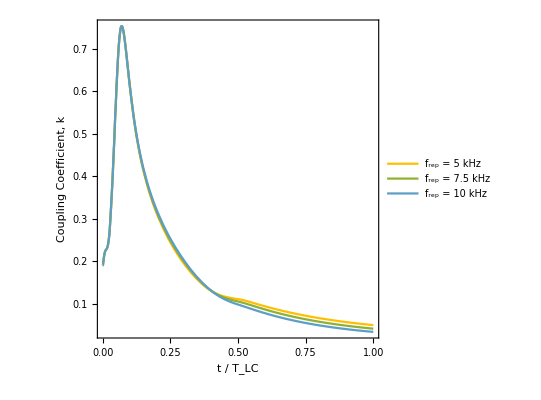

General::munfl: Exp[-1.145×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.1449×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.14468×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

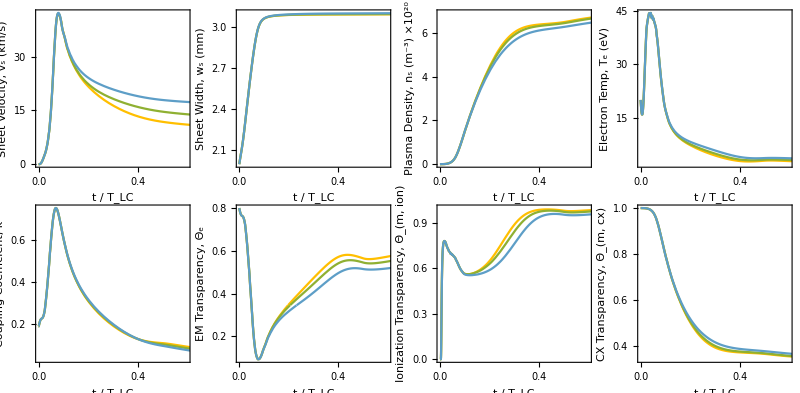

```mathematica
(** Adjust plot styles **)
JPlot[Fun1_,Fun2_,Fun3_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale,Fun3[Τ τLC3]scale},{Τ,0,1},
PlotRange->{{0,0.6},All},
PlotStyle->{ColorData[97,"ColorList"][[8]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[7]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
JkPlot[Fun1_,Fun2_,Fun3_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]/Lc1 scale,Fun2[Τ τLC2]/Lc2 scale,Fun3[Τ τLC3]/Lc3 scale},{Τ,0,1},
PlotRange->{{0,0.6},All},
PlotStyle->{ColorData[97,"ColorList"][[8]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[7]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
EffJPlot[Fun1_,Fun2_,Fun3_,Axislabel_]:=Plot[{Fun1[Τ τLC1]100,Fun2[Τ τLC2]100,Fun3[Τ τLC3]100},{Τ,0,1},
PlotRange->{{0.02,1.0},{0,100}},
PlotStyle->{ColorData[97,"ColorList"][[8]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[7]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];

(** Transparency Calculations **)
za=-0.002; 
ec=1.6 10^-19;   
me=9.11 10^-31; 
kb=1.38 10^-23;  
g0=9.81; 
γ=5/3;  
μ0=4π 10^-7; 
ϵ0=8.85 10^-12;    

SionAr[Te_]:= 2.34 10^-14 Te^0.59 Exp[-17.44/Te]; (* Argon *)
σcxAr= 5 10^-19;
σenAr=4 10^-20;  

ΛAr[ne_,Te_]:=Piecewise[{{23-Log[(ne 10^-6)^(1/2)Te^(-3/2)],Te<7.389},{24-Log[(ne 10^-6)^(1/2)Te^-1],Te≥7.389}}]    (* Coulomb Logarithm *)
νeiAr[ne_,Te_]:=2.91 10^-12 ne Te^(-3/2)ΛAr[ne,Te]  (* e-i collision frequency *)
νenAr[nn_,Te_]:=nn σenAr ((8 ec Te)/(π me))^(1/2)    (*e-n collision frequency *)
ηclAr[ne_,nn_,Te_]:=(me (νeiAr[ne,Te]+νenAr[nn,Te]))/(ne ec^2)   (* Plasma Resistivity - Classical *)
δsdAr[Lterm_,Cp_,ne_,nn_,Te_]:=((2(ηclAr[ne,nn,Te])(Lterm Cp)^(1/2))/μ0)^(1/2)   (* Skin Depth *)

δs1[t_]=δsdAr[L01+Lc1-Mf1[t]^2/Lc1,C01,nsf1[t],nnf1[zsf1[t],t]+nff1[t],Tef1[t]];
δs2[t_]=δsdAr[L02+Lc2-Mf2[t]^2/Lc2,C02,nsf2[t],nnf2[zsf2[t],t]+nff2[t],Tef2[t]];
δs3[t_]=δsdAr[L03+Lc3-Mf3[t]^2/Lc3,C03,nsf3[t],nnf3[zsf3[t],t]+nff3[t],Tef3[t]];

Θs1[t_]=Exp[-3wsf1[t]/δs1[t]];
Θs2[t_]=Exp[-3wsf2[t]/δs2[t]];
Θs3[t_]=Exp[-3wsf3[t]/δs3[t]];

Θmion1[t_]=Exp[(-nsf1[t]wsf1[t]SionAr[Tef1[t]])/vsf1[t]];
Θmion2[t_]=Exp[(-nsf2[t]wsf2[t]SionAr[Tef2[t]])/vsf2[t]];
Θmion3[t_]=Exp[(-nsf3[t]wsf3[t]SionAr[Tef3[t]])/vsf3[t]];

Θmcex1[t_]=Exp[-nsf1[t] wsf1[t]σcxAr];
Θmcex2[t_]=Exp[-nsf2[t] wsf2[t]σcxAr];
Θmcex3[t_]=Exp[-nsf3[t] wsf3[t]σcxAr];

(** Legend Generator **)
Plot[{Mf1[Τ τLC1]/Lc1,Mf2[Τ τLC2]/Lc2,Mf3[Τ τLC3]/Lc3},{Τ,0,1},
PlotRange->{{0,1},All},
PlotStyle->{ColorData[97,"ColorList"][[8]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[7]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC","Coupling Coefficient, k"},
PlotLegends->{"f_rep = 5 kHz", "f_rep = 7.5 kHz","f_rep = 10 kHz"},
Axes->False,
LabelStyle->{18,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]

(** Thesis Output **)
Print[GraphicsGrid[{
{JPlot[vsf1,vsf2,vsf3,"Sheet Velocity, v_s (km/s)",10^-3],JPlot[wsf1,wsf2,wsf3,"Sheet Width, w_s (mm)",10^3],JPlot[nsf1,nsf2,nsf3,"Plasma Density, n_s (m^-3) ×10^20",10^-20],JPlot[Tef1,Tef2,Tef3,"Electron Temp, T_e (eV)",1]},
{JkPlot[Mf1,Mf2,Mf3,"Coupling Coefficient, k",1],JPlot[Θs1,Θs2,Θs3,"EM Transparency, Θ_e",1],JPlot[Θmion1,Θmion2,Θmion3,"Ionization Transparency, Θ_(m, ion)",1],JPlot[Θmcex1,Θmcex2,Θmcex3,"CX Transparency, Θ_(m, cx)",1]}},
Spacings->{5,-5}, ImageSize-> 800]];
```